```mathematica
CF=4/3;
CA=3;
TR=1/2;
β[x_,ξ_]:=√(1-ξ^-1 4 x/(1-x))
xmax[ξ_]:=1/(1+4/ξ)
C2g1[x_,ξ_]:=Piecewise[{{4 TR/(4π)(Log[(1+β[x,ξ])/(1-β[x,ξ])](-8 x^2 ξ^-2-4x ξ^-1(3x-1)+(2 x^2-2x+1))+β[x,ξ](4 ξ^-1 x(x-1)-(8 x^2-8x+1))), x<xmax[ξ]}, {0, x>=xmax[ξ]}}]
CLg1[x_,ξ_]:=Piecewise[{{16 TR/(4π)(x(1-x)β[x,ξ] - 2 x^2 ξ^-1 Log[(1+β[x,ξ])/(1-β[x,ξ])]), x<xmax[ξ]}, {0, x>=xmax[ξ]}}]
Pgq0[x_]:= 2 CF/(4π) pgq[x]
pgq[x_]:=(2/x−2+x)
Pgg0loc[nf_]:=(CA 11/3-2/3 nf)1/(4π)
Pgg0sing[x_]:= (4CA)/(4π) 1/(1-x)
Pgg0reg[x_]:=(4CA)/(4π)(1/x-2+x-x^2)
β0[nf_]:=1/(4π)(11/3 CA-2/3 nf)
```

```mathematica
C2q21[x_,ξ_]:=NIntegrate[1/z C2g1[z,ξ]Pgq0[x/z],{z,x,xmax[ξ]}]
CLq21[x_,ξ_]:=NIntegrate[1/z CLg1[z,ξ]Pgq0[x/z],{z,x,xmax[ξ]}]
```

```mathematica
C2g21reg[x_,ξ_]:=NIntegrate[1/z C2g1[z,ξ]Pgg0reg[x/z],{z,x,xmax[ξ]}]
C2g21loc[x_,ξ_,nf_]:=N[C2g1[x,ξ]Pgg0loc[nf]]
C2g21sing[x_,ξ_]:=NIntegrate[Pgg0sing[z](1/z C2g1[x/z,ξ]-C2g1[x,ξ]),{z,x,1}] -N[C2g1[x,ξ]]NIntegrate[Pgg0sing[z],{z,0,x}] 
C2g21[x_,ξ_]:=C2g21reg[x,ξ]+C2g21sing[x,ξ](*+C2g21loc[x,ξ,nf]-N[β0[nf] C2g1[x,ξ]]*)
```

```mathematica
CLg21reg[x_,ξ_]:=NIntegrate[1/z CLg1[z,ξ]Pgg0reg[x/z],{z,x,1}]
CLg21loc[x_,ξ_,nf_]:=N[CLg1[x,ξ]Pgg0loc[nf]]
CLg21sing[x_,ξ_]:=NIntegrate[Pgg0sing[z](1/z CLg1[x/z,ξ]-CLg1[x,ξ]),{z,x,1}] - N[CLg1[x,ξ]]NIntegrate[Pgg0sing[z],{z,0,x}]
CLg21[x_,ξ_,nf_]:=(CLg21reg[x,ξ]+CLg21loc[x,ξ,nf]+CLg21sing[x,ξ])-N[β0[nf] CLg1[x,ξ]]
CLg21[x_,ξ_]:=CLg21reg[x,ξ]+CLg21sing[x,ξ](*+CLg21loc[x,ξ,nf]-N[β0[nf] CLg1[x,ξ]]*)
```

```mathematica
data2 = Import["/Users/niccololaurenti/Master-thesis/extras/mu_dep_parts/xi=2.dat"];
data20 = Import["/Users/niccololaurenti/Master-thesis/extras/mu_dep_parts/xi=20.dat"];
```

```mathematica
C2g21apfel2=data2[[All,{1,2}]];
C2q21apfel2=data2[[All,{1,3}]];

C2g21apfel20=data20[[All,{1,2}]];
C2q21apfel20=data20[[All,{1,3}]];

CLg21apfel2=data2[[All,{1,4}]];
CLq21apfel2=data2[[All,{1,5}]];

CLg21apfel20=data20[[All,{1,4}]];
CLq21apfel20=data20[[All,{1,5}]];
```

```mathematica
C2g21list2=Table[{x,-C2g21[x,2,3]},{x,0.001,xmax[2],0.001}];
C2g21list20=Table[{x,-C2g21[x,20,3]},{x,0.001,xmax[20],0.001}];
```

```mathematica
CLg21list2=Table[{x,-CLg21[x,2,3]},{x,0.001,xmax[2],0.001}];
CLg21list20=Table[{x,-CLg21[x,20,3]},{x,0.001,xmax[20],0.001}];
```

```mathematica
C2q21list2=Table[{x,-C2q21[x,2]},{x,0.001,xmax[2],0.001}];
C2q21list20=Table[{x,-C2q21[x,20]},{x,0.001,xmax[20],0.001}];
```

```mathematica
CLq21list2=Table[{x,-CLq21[x,2]},{x,0.001,xmax[2],0.001}];
CLq21list20=Table[{x,-CLq21[x,20]},{x,0.001,xmax[20],0.001}];
```

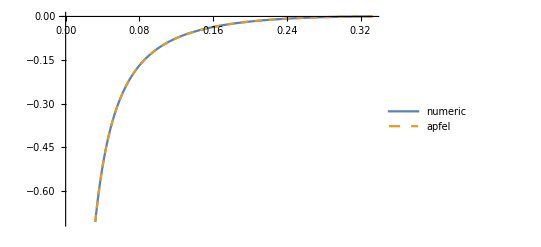

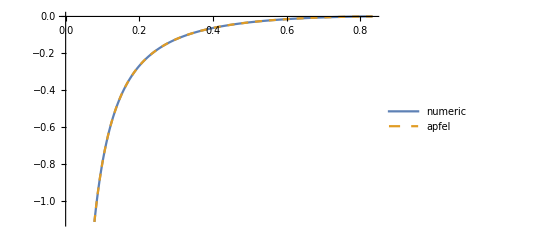

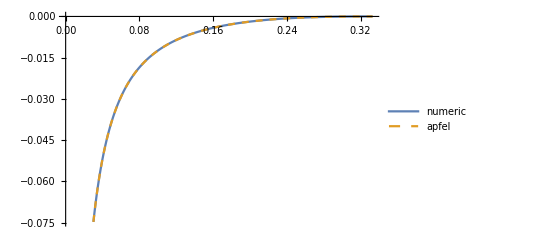

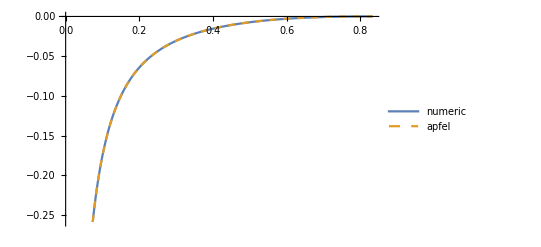

```mathematica
ListLinePlot[{C2q21list2,C2q21apfel2},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed }]
ListLinePlot[{C2q21list20,C2q21apfel20},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed  }]
ListLinePlot[{CLq21list2,CLq21apfel2},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed }]
ListLinePlot[{CLq21list20,CLq21apfel20},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed }]
```

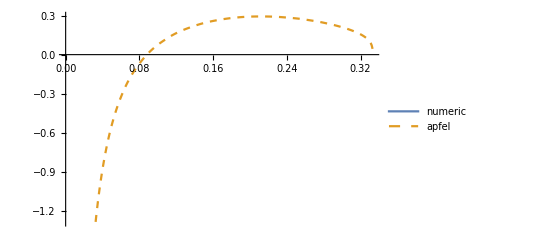

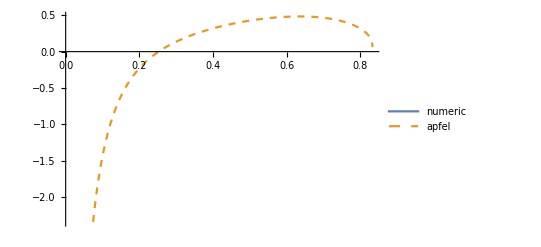

```mathematica
ListLinePlot[{C2g21list2,C2g21apfel2},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed  }]
ListLinePlot[{C2g21list20, C2g21apfel20},PlotLegends->{"numeric","apfel"}, PlotStyle->{,Dashed  }]
```

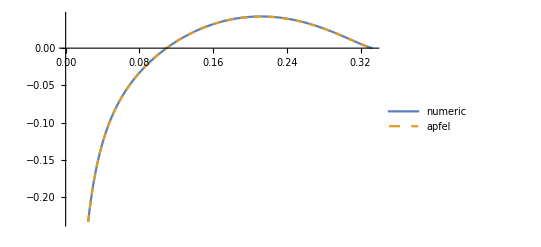

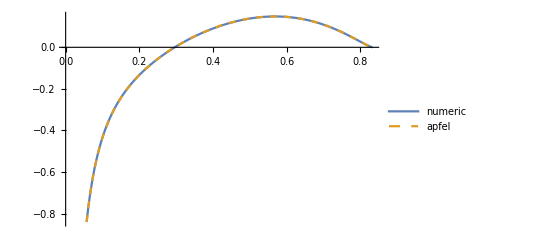

```mathematica
ListLinePlot[{CLg21list2,CLg21apfel2},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed  }]
ListLinePlot[{CLg21list20, CLg21apfel20},PlotLegends->{"numeric","apfel"}, PlotStyle->{,Dashed  }]
```

```mathematica
<<HPL`
```

Package HPL already loaded...

$Aborted

```mathematica
pggreg[x_]:= 1/x-2+x-x^2
pggsing[x_]:=1/(1-x)
```

```mathematica
Pgg1reg[x_,nf_]:=(4 CA nf(1-x-10/9pggreg[x]-13/9(1/x-x*x)-2/3(1+x)HPL[{0},x])+4 CA^2(27+(1+x)(11/3HPL[{0},x]+8HPL[{0,0},x]-27/2)+2(pggreg[-x]+pggsing[-x])(HPL[{0,0},x]-2HPL[{-1,0},x]-Zeta[2])-67/9(1/x-x*x)-12HPL[{0},x]-44/3x*x HPL[{0},x]+2pggreg[x](67/18-Zeta[2]+HPL[{0,0},x]+2HPL[{1,0},x]+2HPL[{0,1},x])+2((67/18-Zeta[2]+HPL[{0,0},x]+2HPL[{1,0},x]+2HPL[{0,1},x])-(67/18-Zeta[2]))pggsing[x]) +4CF nf (2HPL[{0},x]+2/3/x+10/3x*x-12+(1+x)(4-5HPL[{0},x]-2HPL[{0,0},x])))/16/π^2
Pgg1sing[x_,nf_]:= (4 CA nf(-10/9 pggsing[x])+4 CA^2(2pggsing[x](67/18-Zeta[2])))/16/π^2
Pgg1loc[nf_]:=4(-2/3  CA nf+(8/3+3Zeta[3])CA CA-1/2CF nf)/16/π^2
```

```mathematica
C2g31reg[x_,ξ_,nf_]:=NIntegrate[1/z C2g1[z,ξ]Pgg1reg[x/z,nf],{z,x,xmax[ξ]}]
C2g31loc[x_,ξ_,nf_]:=N[C2g1[x,ξ]Pgg1loc[nf]]
C2g31sing[x_,ξ_,nf_]:=NIntegrate[Pgg1sing[z,nf](1/z C2g1[x/z,ξ]-C2g1[x,ξ]),{z,x,1}] -N[C2g1[x,ξ]]NIntegrate[Pgg1sing[z,nf],{z,0,x}] 
C2g31xPgg1[x_,ξ_,nf_]:=C2g31reg[x,ξ,nf]+C2g31sing[x,ξ,nf]+C2g31loc[x,ξ,nf]
```

```mathematica
C2g31xPgg1[0.1,2,3]
```

0.1099+2.35314×10^-27 ⅈ

```mathematica
C2g31list2=Table[{x,-C2g31xPgg1[x,2,3]},{x,0.001,1-0.001,0.001}];
```

```mathematica
Pgg1reglist=Table[{x,Pgg1reg[x,3]},{x,0.001,1-0.001,0.001}];
```

```mathematica
C2g31list2
```

{{0.001,29.3357},{0.002,10.8096},{0.003,5.39881},{0.004,2.99344},{0.005,1.70327},{0.006,0.933093},{0.007,0.440815},{0.008,0.111235},{0.009,-0.11666},{0.01,-0.277811},{0.011,-0.393457+4.90134×10^-17 ⅈ},{0.012,-0.477127},{0.013,-0.537775+3.96747×10^-17 ⅈ},{0.014,-0.581515},{0.015,-0.612632+3.30407×10^-17 ⅈ},{0.016,-0.634197},{0.017,-0.648454},{0.018,-0.657069},{0.019,-0.661297+1.50131×10^-28 ⅈ},{0.02,-0.662095},{0.021,-0.660202},{0.022,-0.656193+2.00413×10^-17 ⅈ},{0.023,-0.650519+1.88903×10^-17 ⅈ},{0.024,-0.643537},{0.025,-0.635533},{0.026,-0.626735+1.60243×10^-17 ⅈ},{0.027,-0.617325},{0.028,-0.607452},{0.029,-0.597237},{0.03,-0.586777+1.31862×10^-17 ⅈ},{0.031,-0.576153+1.26041×10^-17 ⅈ},{0.032,-0.56543},{0.033,-0.55466},{0.034,-0.543888},{0.035,-0.533149},{0.036,-0.522472+6.31804×10^-29 ⅈ},{0.037,-0.51188},{0.038,-0.501393+9.47915×10^-18 ⅈ},{0.039,-0.491026+9.13502×10^-18 ⅈ},{0.04,-0.480791},{0.041,-0.470697},{0.042,-0.460752},{0.043,-0.450962+7.9381×10^-18 ⅈ},{0.044,-0.44133+7.6772×10^-18 ⅈ},{0.045,-0.43186+7.42944×10^-18 ⅈ},{0.046,-0.422553+7.19388×10^-18 ⅈ},{0.047,-0.413411},{0.048,-0.404432},{0.049,-0.395618},{0.05,-0.386966},{0.051,-0.378477+6.17222×10^-18 ⅈ},{0.052,-0.370147+5.99459×10^-18 ⅈ},{0.053,-0.361975+5.82459×10^-18 ⅈ},{0.054,-0.353959+5.66177×10^-18 ⅈ},{0.055,-0.346097},{0.056,-0.338385},{0.057,-0.330822},{0.058,-0.323404},{0.059,-0.31613+4.94152×10^-18 ⅈ},{0.06,-0.308995+4.81387×10^-18 ⅈ},{0.061,-0.301998+4.69101×10^-18 ⅈ},{0.062,-0.295135+4.5727×10^-18 ⅈ},{0.063,-0.288404},{0.064,-0.281802},{0.065,-0.275326},{0.066,-0.268973},{0.067,-0.262741},{0.068,-0.256627},{0.069,-0.250628},{0.07,-0.244742},{0.071,-0.238967+3.83995×10^-16 ⅈ},{0.072,-0.233299+2.2193×10^-29 ⅈ},{0.073,-0.227736},{0.074,-0.222277+3.43493×10^-18 ⅈ},{0.075,-0.216918+3.35889×10^-18 ⅈ},{0.076,-0.211657+3.28515×10^-18 ⅈ},{0.077,-0.206493+3.21364×10^-18 ⅈ},{0.078,-0.201422+3.14424×10^-18 ⅈ},{0.079,-0.196444},{0.08,-0.191555},{0.081,-0.186754},{0.082,-0.182039},{0.083,-0.177408},{0.084,-0.172859},{0.085,-0.16839},{0.086,-0.164+2.77278×10^-16 ⅈ},{0.087,-0.159687+2.71667×10^-16 ⅈ},{0.088,-0.155448+2.66204×10^-16 ⅈ},{0.089,-0.151284+2.49882×10^-18 ⅈ},{0.09,-0.147191+2.44919×10^-18 ⅈ},{0.091,-0.143169+2.40083×10^-18 ⅈ},{0.092,-0.139215+2.3537×10^-18 ⅈ},{0.093,-0.135329+2.30776×10^-18 ⅈ},{0.094,-0.131509},{0.095,-0.127753},{0.096,-0.124061},{0.097,-0.120431},{0.098,-0.116862},{0.099,-0.113351},{0.1,-0.1099-2.35314×10^-27 ⅈ},{0.101,-0.106505-2.01766×10^-27 ⅈ},{0.102,-0.103166+2.02689×10^-16 ⅈ},{0.103,-0.0998816+1.98922×10^-16 ⅈ},{0.104,-0.0966511+1.95241×10^-16 ⅈ},{0.105,-0.0934732+1.8356×10^-18 ⅈ},{0.106,-0.0903468+1.80191×10^-18 ⅈ},{0.107,-0.0872711+1.76896×10^-18 ⅈ},{0.108,-0.0842449+1.73674×10^-18 ⅈ},{0.109,-0.0812674+1.70522×10^-18 ⅈ},{0.11,-0.0783376},{0.111,-0.0754545},{0.112,-0.0726174},{0.113,-0.0698253},{0.114,-0.0670774},{0.115,-0.0643729-2.22481×10^-25 ⅈ},{0.116,-0.0617109-5.52484×10^-27 ⅈ},{0.117,-0.0590908-5.14081×10^-27 ⅈ},{0.118,-0.0565117+1.51379×10^-16 ⅈ},{0.119,-0.0539728+1.48715×10^-16 ⅈ},{0.12,-0.0514736+1.46104×10^-16 ⅈ},{0.121,-0.0490132+1.37491×10^-18 ⅈ},{0.122,-0.0465909+1.35088×10^-18 ⅈ},{0.123,-0.0442062+1.32733×10^-18 ⅈ},{0.124,-0.0418583+1.30423×10^-18 ⅈ},{0.125,-0.0395466},{0.126,-0.0372705},{0.127,-0.0350294},{0.128,-0.0328226},{0.129,-0.0306496},{0.13,-0.0285098},{0.131,-0.0264028},{0.132,-0.0243278},{0.133,-0.0222844},{0.134,-0.0202721},{0.135,-0.0182904},{0.136,-0.0163388-4.5509×10^-27 ⅈ},{0.137,-0.0144168-4.26527×10^-27 ⅈ},{0.138,-0.0125239-3.97198×10^-27 ⅈ},{0.139,-0.0106597-3.66861×10^-27 ⅈ},{0.14,-0.00882367-3.3518×10^-27 ⅈ},{0.141,-0.00701546+1.01463×10^-16 ⅈ},{0.142,-0.00523459+9.97378×10^-17 ⅈ},{0.143,-0.00348066},{0.144,-0.00175327},{0.145,-0.000051986},{0.146,0.00162356+9.3134×10^-17 ⅈ},{0.147,0.00327376+9.15537×10^-17 ⅈ},{0.148,0.00489899+9.00003×10^-17 ⅈ},{0.149,0.00649961+8.84733×10^-17 ⅈ},{0.15,0.00807599+8.69722×10^-17 ⅈ},{0.151,0.00962848+8.54964×10^-17 ⅈ},{0.152,0.0111574+8.40454×10^-17 ⅈ},{0.153,0.0126631+7.9134×10^-19 ⅈ},{0.154,0.014146+7.77902×10^-19 ⅈ},{0.155,0.0156062+7.64686×10^-19 ⅈ},{0.156,0.0170443+7.51689×10^-19 ⅈ},{0.157,0.0184604-3.63848×10^-27 ⅈ},{0.158,0.0198548-3.41184×10^-27 ⅈ},{0.159,0.0212279-3.17798×10^-27 ⅈ},{0.16,0.02258-2.93483×10^-27 ⅈ},{0.161,0.0239112-2.67948×10^-27 ⅈ},{0.162,0.025222-2.40765×10^-27 ⅈ},{0.163,0.0265126-2.11257×10^-27 ⅈ},{0.164,0.0277832-1.78222×10^-27 ⅈ},{0.165,0.0290341-1.39112×10^-27 ⅈ},{0.166,0.0302656-8.59089×10^-28 ⅈ},{0.167,0.0314779},{0.168,0.0326712},{0.169,0.0338459},{0.17,0.035002},{0.171,0.03614},{0.172,0.0372599+1.13446×10^-18 ⅈ},{0.173,0.038362+1.11481×10^-18 ⅈ},{0.174,0.0394465+1.09546×10^-18 ⅈ},{0.175,0.0405137+1.07641×10^-18 ⅈ},{0.176,0.0415637+1.05765×10^-18 ⅈ},{0.177,0.0425968+1.03919×10^-18 ⅈ},{0.178,0.0436131+1.02101×10^-18 ⅈ},{0.179,0.0446128+1.00311×10^-18 ⅈ},{0.18,0.0455962+9.8549×10^-19 ⅈ},{0.181,0.0465633+9.68137×10^-19 ⅈ},{0.182,0.0475145+9.51051×10^-19 ⅈ},{0.183,0.0484499+9.34225×10^-19 ⅈ},{0.184,0.0493696+9.17657×10^-19 ⅈ},{0.185,0.0502739+9.01341×10^-19 ⅈ},{0.186,0.0511629+8.85273×10^-19 ⅈ},{0.187,0.0520367+8.69449×10^-19 ⅈ},{0.188,0.0528956-4.03143×10^-27 ⅈ},{0.189,0.0537397-3.89977×10^-27 ⅈ},{0.19,0.0545691-3.7675×10^-27 ⅈ},{0.191,0.055384-3.63444×10^-27 ⅈ},{0.192,0.0561846-3.50037×10^-27 ⅈ},{0.193,0.056971-3.36504×10^-27 ⅈ},{0.194,0.0577434-3.22816×10^-27 ⅈ},{0.195,0.0585018-3.0894×10^-27 ⅈ},{0.196,0.0592465-2.94837×10^-27 ⅈ},{0.197,0.0599775-2.80458×10^-27 ⅈ},{0.198,0.0606951-2.65746×10^-27 ⅈ},{0.199,0.0613993-2.50628×10^-27 ⅈ},{0.2,0.0620902-2.35011×10^-27 ⅈ},{0.201,0.0627681-2.18774×10^-27 ⅈ},{0.202,0.0634329-2.01751×10^-27 ⅈ},{0.203,0.0640849-1.83708×10^-27 ⅈ},{0.204,0.0647242+6.34189×10^-19 ⅈ},{0.205,0.0653509+6.22146×10^-19 ⅈ},{0.206,0.065965+6.10282×10^-19 ⅈ},{0.207,0.0665667+5.98597×10^-19 ⅈ},{0.208,0.0671562+5.87087×10^-19 ⅈ},{0.209,0.0677335+5.75749×10^-19 ⅈ},{0.21,0.0682987+5.64581×10^-19 ⅈ},{0.211,0.0688519+5.53581×10^-19 ⅈ},{0.212,0.0693933+5.42747×10^-19 ⅈ},{0.213,0.0699229+5.32075×10^-19 ⅈ},{0.214,0.0704408+5.21563×10^-19 ⅈ},{0.215,0.0709472+5.1121×10^-19 ⅈ},{0.216,0.0714421+5.01013×10^-19 ⅈ},{0.217,0.0719256+4.90969×10^-19 ⅈ},{0.218,0.0723979+4.81077×10^-19 ⅈ},{0.219,0.0728589},{0.22,0.0733088},{0.221,0.0737477},{0.222,0.0741756},{0.223,0.0745926},{0.224,0.0749989},{0.225,0.0753945},{0.226,0.0757794},{0.227,0.0761538},{0.228,0.0765176},{0.229,0.0768711},{0.23,0.0772142-2.95526×10^-27 ⅈ},{0.231,0.0775471-2.86169×10^-27 ⅈ},{0.232,0.0778697-2.76731×10^-27 ⅈ},{0.233,0.0781822-2.67198×10^-27 ⅈ},{0.234,0.0784846-2.57553×10^-27 ⅈ},{0.235,0.078777+3.34205×10^-19 ⅈ},{0.236,0.0790594+3.26715×10^-19 ⅈ},{0.237,0.0793319+3.19343×10^-19 ⅈ},{0.238,0.0795946+3.12088×10^-19 ⅈ},{0.239,0.0798475+3.04946×10^-19 ⅈ},{0.24,0.0800906+2.97918×10^-19 ⅈ},{0.241,0.080324+2.91001×10^-19 ⅈ},{0.242,0.0805479+2.84195×10^-19 ⅈ},{0.243,0.0807621+2.77497×10^-19 ⅈ},{0.244,0.0809668+2.70907×10^-19 ⅈ},{0.245,0.081162+2.64424×10^-19 ⅈ},{0.246,0.0813477+2.58045×10^-19 ⅈ},{0.247,0.081524+2.51769×10^-19 ⅈ},{0.248,0.081691+2.45597×10^-19 ⅈ},{0.249,0.0818486+2.39525×10^-19 ⅈ},{0.25,0.0819969},{0.251,0.082136},{0.252,0.0822658},{0.253,0.0823864},{0.254,0.0824979},{0.255,0.0826002},{0.256,0.0826934},{0.257,0.0827775},{0.258,0.0828525},{0.259,0.0829184},{0.26,0.0829753},{0.261,0.0830232},{0.262,0.0830621},{0.263,0.0830919},{0.264,0.0831128},{0.265,0.0831246},{0.266,0.0831274},{0.267,0.0831212},{0.268,0.083106},{0.269,0.0830818},{0.27,0.0830485},{0.271,0.0830061-2.34933×10^-27 ⅈ},{0.272,0.0829546-2.27913×10^-27 ⅈ},{0.273,0.0828941-2.20822×10^-27 ⅈ},{0.274,0.0828243-2.13648×10^-27 ⅈ},{0.275,0.0827454-2.0638×10^-27 ⅈ},{0.276,0.0826573-1.99003×10^-27 ⅈ},{0.277,0.0825599-1.91502×10^-27 ⅈ},{0.278,0.0824531-1.83858×10^-27 ⅈ},{0.279,0.0823369-1.76049×10^-27 ⅈ},{0.28,0.0822113-1.68048×10^-27 ⅈ},{0.281,0.0820761-1.59823×10^-27 ⅈ},{0.282,0.0819313+8.88549×10^-20 ⅈ},{0.283,0.0817767+8.561×10^-20 ⅈ},{0.284,0.0816123+8.24333×10^-20 ⅈ},{0.285,0.081438+7.93242×10^-20 ⅈ},{0.286,0.0812535+4.73401×10^-31 ⅈ},{0.287,0.0810589+4.54932×10^-31 ⅈ},{0.288,0.0808539-9.33505×10^-45 ⅈ},{0.289,0.0806383+4.19211×10^-31 ⅈ},{0.29,0.080412+6.47687×10^-20 ⅈ},{0.291,0.0801748+6.20511×10^-20 ⅈ},{0.292,0.0799265+5.93966×10^-20 ⅈ},{0.293,0.0796667+5.68045×10^-20 ⅈ},{0.294,0.0793952+5.42743×10^-20 ⅈ},{0.295,0.0791118+5.18053×10^-20 ⅈ},{0.296,0.0788161+4.93971×10^-20 ⅈ},{0.297,0.0785078+4.70491×10^-20 ⅈ},{0.298,0.0781863+4.47607×10^-20 ⅈ},{0.299,0.0778514+4.25314×10^-20 ⅈ},{0.3,0.0775025+4.03608×10^-20 ⅈ},{0.301,0.0771391+3.82482×10^-20 ⅈ},{0.302,0.0767605+3.61934×10^-20 ⅈ},{0.303,0.0763662+3.41957×10^-20 ⅈ},{0.304,0.0759553+3.22547×10^-20 ⅈ},{0.305,0.0755271+3.03701×10^-20 ⅈ},{0.306,0.0750806+2.85414×10^-20 ⅈ},{0.307,0.0746147+2.67682×10^-20 ⅈ},{0.308,0.0741282+2.50501×10^-20 ⅈ},{0.309,0.0736199+2.33868×10^-20 ⅈ},{0.31,0.0730882+2.17781×10^-20 ⅈ},{0.311,0.0725313+2.02235×10^-20 ⅈ},{0.312,0.0719473+1.87229×10^-20 ⅈ},{0.313,0.0713338-1.87773×10^-27 ⅈ},{0.314,0.0706882-1.82224×10^-27 ⅈ},{0.315,0.0700073-1.76604×10^-27 ⅈ},{0.316,0.0692875-1.70906×10^-27 ⅈ},{0.317,0.0685244-1.65118×10^-27 ⅈ},{0.318,0.0677128-1.59229×10^-27 ⅈ},{0.319,0.0668466-1.53226×10^-27 ⅈ},{0.32,0.065918-1.47092×10^-27 ⅈ},{0.321,0.0649177-1.40808×10^-27 ⅈ},{0.322,0.0638339-1.34351×10^-27 ⅈ},{0.323,0.0626515-1.27692×10^-27 ⅈ},{0.324,0.0613511-1.20794×10^-27 ⅈ},{0.325,0.0599067-1.13614×10^-27 ⅈ},{0.326,0.0582828-1.06089×10^-27 ⅈ},{0.327,0.0564287-9.81387×10^-28 ⅈ},{0.328,0.0542695-8.96467×10^-28 ⅈ},{0.329,0.0516857-8.04383×10^-28 ⅈ},{0.33,0.0484714-7.02286×10^-28 ⅈ},{0.331,0.0442179-5.84914×10^-28 ⅈ},{0.332,0.0378976-4.40157×10^-28 ⅈ},{0.333,0.0246884-2.19088×10^-28 ⅈ},{0.334,0.},{0.335,0.},{0.336,0.},{0.337,0.},{0.338,0.},{0.339,0.},{0.34,0.},{0.341,0.},{0.342,0.},{0.343,0.},{0.344,0.},{0.345,0.},{0.346,0.},{0.347,0.},{0.348,0.},{0.349,0.},{0.35,0.},{0.351,0.},{0.352,0.},{0.353,0.},{0.354,0.},{0.355,0.},{0.356,0.},{0.357,0.},{0.358,0.},{0.359,0.},{0.36,0.},{0.361,0.},{0.362,0.},{0.363,0.},{0.364,0.},{0.365,0.},{0.366,0.},{0.367,0.},{0.368,0.},{0.369,0.},{0.37,0.},{0.371,0.},{0.372,0.},{0.373,0.},{0.374,0.},{0.375,0.},{0.376,0.},{0.377,0.},{0.378,0.},{0.379,0.},{0.38,0.},{0.381,0.},{0.382,0.},{0.383,0.},{0.384,0.},{0.385,0.},{0.386,0.},{0.387,0.},{0.388,0.},{0.389,0.},{0.39,0.},{0.391,0.},{0.392,0.},{0.393,0.},{0.394,0.},{0.395,0.},{0.396,0.},{0.397,0.},{0.398,0.},{0.399,0.},{0.4,0.},{0.401,0.},{0.402,0.},{0.403,0.},{0.404,0.},{0.405,0.},{0.406,0.},{0.407,0.},{0.408,0.},{0.409,0.},{0.41,0.},{0.411,0.},{0.412,0.},{0.413,0.},{0.414,0.},{0.415,0.},{0.416,0.},{0.417,0.},{0.418,0.},{0.419,0.},{0.42,0.},{0.421,0.},{0.422,0.},{0.423,0.},{0.424,0.},{0.425,0.},{0.426,0.},{0.427,0.},{0.428,0.},{0.429,0.},{0.43,0.},{0.431,0.},{0.432,0.},{0.433,0.},{0.434,0.},{0.435,0.},{0.436,0.},{0.437,0.},{0.438,0.},{0.439,0.},{0.44,0.},{0.441,0.},{0.442,0.},{0.443,0.},{0.444,0.},{0.445,0.},{0.446,0.},{0.447,0.},{0.448,0.},{0.449,0.},{0.45,0.},{0.451,0.},{0.452,0.},{0.453,0.},{0.454,0.},{0.455,0.},{0.456,0.},{0.457,0.},{0.458,0.},{0.459,0.},{0.46,0.},{0.461,0.},{0.462,0.},{0.463,0.},{0.464,0.},{0.465,0.},{0.466,0.},{0.467,0.},{0.468,0.},{0.469,0.},{0.47,0.},{0.471,0.},{0.472,0.},{0.473,0.},{0.474,0.},{0.475,0.},{0.476,0.},{0.477,0.},{0.478,0.},{0.479,0.},{0.48,0.},{0.481,0.},{0.482,0.},{0.483,0.},{0.484,0.},{0.485,0.},{0.486,0.},{0.487,0.},{0.488,0.},{0.489,0.},{0.49,0.},{0.491,0.},{0.492,0.},{0.493,0.},{0.494,0.},{0.495,0.},{0.496,0.},{0.497,0.},{0.498,0.},{0.499,0.},{0.5,0.},{0.501,0.},{0.502,0.},{0.503,0.},{0.504,0.},{0.505,0.},{0.506,0.},{0.507,0.},{0.508,0.},{0.509,0.},{0.51,0.},{0.511,0.},{0.512,0.},{0.513,0.},{0.514,0.},{0.515,0.},{0.516,0.},{0.517,0.},{0.518,0.},{0.519,0.},{0.52,0.},{0.521,0.},{0.522,0.},{0.523,0.},{0.524,0.},{0.525,0.},{0.526,0.},{0.527,0.},{0.528,0.},{0.529,0.},{0.53,0.},{0.531,0.},{0.532,0.},{0.533,0.},{0.534,0.},{0.535,0.},{0.536,0.},{0.537,0.},{0.538,0.},{0.539,0.},{0.54,0.},{0.541,0.},{0.542,0.},{0.543,0.},{0.544,0.},{0.545,0.},{0.546,0.},{0.547,0.},{0.548,0.},{0.549,0.},{0.55,0.},{0.551,0.},{0.552,0.},{0.553,0.},{0.554,0.},{0.555,0.},{0.556,0.},{0.557,0.},{0.558,0.},{0.559,0.},{0.56,0.},{0.561,0.},{0.562,0.},{0.563,0.},{0.564,0.},{0.565,0.},{0.566,0.},{0.567,0.},{0.568,0.},{0.569,0.},{0.57,0.},{0.571,0.},{0.572,0.},{0.573,0.},{0.574,0.},{0.575,0.},{0.576,0.},{0.577,0.},{0.578,0.},{0.579,0.},{0.58,0.},{0.581,0.},{0.582,0.},{0.583,0.},{0.584,0.},{0.585,0.},{0.586,0.},{0.587,0.},{0.588,0.},{0.589,0.},{0.59,0.},{0.591,0.},{0.592,0.},{0.593,0.},{0.594,0.},{0.595,0.},{0.596,0.},{0.597,0.},{0.598,0.},{0.599,0.},{0.6,0.},{0.601,0.},{0.602,0.},{0.603,0.},{0.604,0.},{0.605,0.},{0.606,0.},{0.607,0.},{0.608,0.},{0.609,0.},{0.61,0.},{0.611,0.},{0.612,0.},{0.613,0.},{0.614,0.},{0.615,0.},{0.616,0.},{0.617,0.},{0.618,0.},{0.619,0.},{0.62,0.},{0.621,0.},{0.622,0.},{0.623,0.},{0.624,0.},{0.625,0.},{0.626,0.},{0.627,0.},{0.628,0.},{0.629,0.},{0.63,0.},{0.631,0.},{0.632,0.},{0.633,0.},{0.634,0.},{0.635,0.},{0.636,0.},{0.637,0.},{0.638,0.},{0.639,0.},{0.64,0.},{0.641,0.},{0.642,0.},{0.643,0.},{0.644,0.},{0.645,0.},{0.646,0.},{0.647,0.},{0.648,0.},{0.649,0.},{0.65,0.},{0.651,0.},{0.652,0.},{0.653,0.},{0.654,0.},{0.655,0.},{0.656,0.},{0.657,0.},{0.658,0.},{0.659,0.},{0.66,0.},{0.661,0.},{0.662,0.},{0.663,0.},{0.664,0.},{0.665,0.},{0.666,0.},{0.667,0.},{0.668,0.},{0.669,0.},{0.67,0.},{0.671,0.},{0.672,0.},{0.673,0.},{0.674,0.},{0.675,0.},{0.676,0.},{0.677,0.},{0.678,0.},{0.679,0.},{0.68,0.},{0.681,0.},{0.682,0.},{0.683,0.},{0.684,0.},{0.685,0.},{0.686,0.},{0.687,0.},{0.688,0.},{0.689,0.},{0.69,0.},{0.691,0.},{0.692,0.},{0.693,0.},{0.694,0.},{0.695,0.},{0.696,0.},{0.697,0.},{0.698,0.},{0.699,0.},{0.7,0.},{0.701,0.},{0.702,0.},{0.703,0.},{0.704,0.},{0.705,0.},{0.706,0.},{0.707,0.},{0.708,0.},{0.709,0.},{0.71,0.},{0.711,0.},{0.712,0.},{0.713,0.},{0.714,0.},{0.715,0.},{0.716,0.},{0.717,0.},{0.718,0.},{0.719,0.},{0.72,0.},{0.721,0.},{0.722,0.},{0.723,0.},{0.724,0.},{0.725,0.},{0.726,0.},{0.727,0.},{0.728,0.},{0.729,0.},{0.73,0.},{0.731,0.},{0.732,0.},{0.733,0.},{0.734,0.},{0.735,0.},{0.736,0.},{0.737,0.},{0.738,0.},{0.739,0.},{0.74,0.},{0.741,0.},{0.742,0.},{0.743,0.},{0.744,0.},{0.745,0.},{0.746,0.},{0.747,0.},{0.748,0.},{0.749,0.},{0.75,0.},{0.751,0.},{0.752,0.},{0.753,0.},{0.754,0.},{0.755,0.},{0.756,0.},{0.757,0.},{0.758,0.},{0.759,0.},{0.76,0.},{0.761,0.},{0.762,0.},{0.763,0.},{0.764,0.},{0.765,0.},{0.766,0.},{0.767,0.},{0.768,0.},{0.769,0.},{0.77,0.},{0.771,0.},{0.772,0.},{0.773,0.},{0.774,0.},{0.775,0.},{0.776,0.},{0.777,0.},{0.778,0.},{0.779,0.},{0.78,0.},{0.781,0.},{0.782,0.},{0.783,0.},{0.784,0.},{0.785,0.},{0.786,0.},{0.787,0.},{0.788,0.},{0.789,0.},{0.79,0.},{0.791,0.},{0.792,0.},{0.793,0.},{0.794,0.},{0.795,0.},{0.796,0.},{0.797,0.},{0.798,0.},{0.799,0.},{0.8,0.},{0.801,0.},{0.802,0.},{0.803,0.},{0.804,0.},{0.805,0.},{0.806,0.},{0.807,0.},{0.808,0.},{0.809,0.},{0.81,0.},{0.811,0.},{0.812,0.},{0.813,0.},{0.814,0.},{0.815,0.},{0.816,0.},{0.817,0.},{0.818,0.},{0.819,0.},{0.82,0.},{0.821,0.},{0.822,0.},{0.823,0.},{0.824,0.},{0.825,0.},{0.826,0.},{0.827,0.},{0.828,0.},{0.829,0.},{0.83,0.},{0.831,0.},{0.832,0.},{0.833,0.},{0.834,0.},{0.835,0.},{0.836,0.},{0.837,0.},{0.838,0.},{0.839,0.},{0.84,0.},{0.841,0.},{0.842,0.},{0.843,0.},{0.844,0.},{0.845,0.},{0.846,0.},{0.847,0.},{0.848,0.},{0.849,0.},{0.85,0.},{0.851,0.},{0.852,0.},{0.853,0.},{0.854,0.},{0.855,0.},{0.856,0.},{0.857,0.},{0.858,0.},{0.859,0.},{0.86,0.},{0.861,0.},{0.862,0.},{0.863,0.},{0.864,0.},{0.865,0.},{0.866,0.},{0.867,0.},{0.868,0.},{0.869,0.},{0.87,0.},{0.871,0.},{0.872,0.},{0.873,0.},{0.874,0.},{0.875,0.},{0.876,0.},{0.877,0.},{0.878,0.},{0.879,0.},{0.88,0.},{0.881,0.},{0.882,0.},{0.883,0.},{0.884,0.},{0.885,0.},{0.886,0.},{0.887,0.},{0.888,0.},{0.889,0.},{0.89,0.},{0.891,0.},{0.892,0.},{0.893,0.},{0.894,0.},{0.895,0.},{0.896,0.},{0.897,0.},{0.898,0.},{0.899,0.},{0.9,0.},{0.901,0.},{0.902,0.},{0.903,0.},{0.904,0.},{0.905,0.},{0.906,0.},{0.907,0.},{0.908,0.},{0.909,0.},{0.91,0.},{0.911,0.},{0.912,0.},{0.913,0.},{0.914,0.},{0.915,0.},{0.916,0.},{0.917,0.},{0.918,0.},{0.919,0.},{0.92,0.},{0.921,0.},{0.922,0.},{0.923,0.},{0.924,0.},{0.925,0.},{0.926,0.},{0.927,0.},{0.928,0.},{0.929,0.},{0.93,0.},{0.931,0.},{0.932,0.},{0.933,0.},{0.934,0.},{0.935,0.},{0.936,0.},{0.937,0.},{0.938,0.},{0.939,0.},{0.94,0.},{0.941,0.},{0.942,0.},{0.943,0.},{0.944,0.},{0.945,0.},{0.946,0.},{0.947,0.},{0.948,0.},{0.949,0.},{0.95,0.},{0.951,0.},{0.952,0.},{0.953,0.},{0.954,0.},{0.955,0.},{0.956,0.},{0.957,0.},{0.958,0.},{0.959,0.},{0.96,0.},{0.961,0.},{0.962,0.},{0.963,0.},{0.964,0.},{0.965,0.},{0.966,0.},{0.967,0.},{0.968,0.},{0.969,0.},{0.97,0.},{0.971,0.},{0.972,0.},{0.973,0.},{0.974,0.},{0.975,0.},{0.976,0.},{0.977,0.},{0.978,0.},{0.979,0.},{0.98,0.},{0.981,0.},{0.982,0.},{0.983,0.},{0.984,0.},{0.985,0.},{0.986,0.},{0.987,0.},{0.988,0.},{0.989,0.},{0.99,0.},{0.991,0.},{0.992,0.},{0.993,0.},{0.994,0.},{0.995,0.},{0.996,0.},{0.997,0.},{0.998,0.},{0.999,0.}}

```mathematica
prova2 = Import["/Users/niccololaurenti/Master-thesis/extras/mu_dep_parts/prova.dat"];
C2g31list2code=prova2[[All,{1,2}]];
```

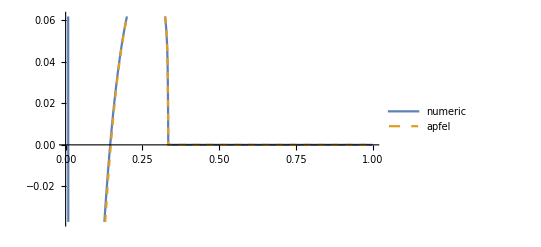

```mathematica
ListLinePlot[{C2g31list2,C2g31list2code},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed  }]
```

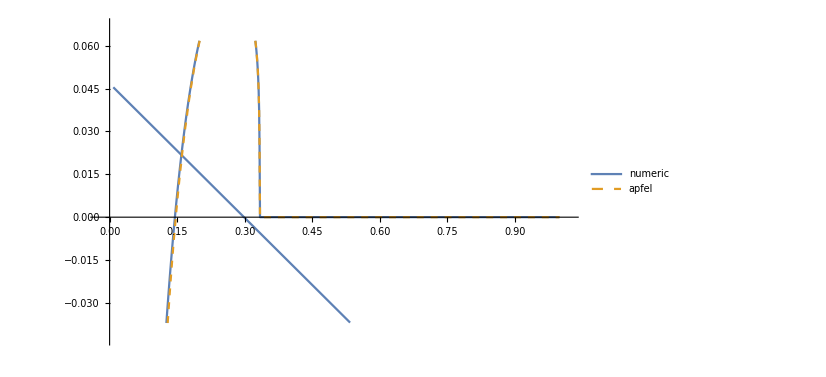

```mathematica
Pgg1reglist-C2g31list2code
```

{{0.,0.000105877},{0.,-0.0000946376},{0.,0.000345106},{0.,0.000124996},{0.,0.000445499},{0.,0.0000255809},{0.,-0.0000313115},{0.,0.0000192497},{1.73472×10^-18,-5.55054×10^-7},{1.73472×10^-18,-0.0000250258},{0.,0.000014116},{0.,-5.75998×10^-6},{1.73472×10^-18,3.90667×10^-6},{1.73472×10^-18,0.0000374991},{0.,0.0000164915},{0.,-0.0000445321},{0.,0.0000300882},{3.46945×10^-18,0.0000235161},{3.46945×10^-18,6.29996×10^-6},{0.,-0.0000371981},{0.,-0.0000181395},{3.46945×10^-18,0.0000138923},{0.,0.0000263242},{0.,0.0000453049},{0.,0.0000435062},{3.46945×10^-18,0.0000154316},{3.46945×10^-18,-0.0000306178},{0.,-0.0000430975},{0.,-0.0000452082},{3.46945×10^-18,0.0000107394},{0.,-0.0000392042},{0.,0.000024835},{0.,-0.0000153257},{0.,0.0000484204},{0.,3.79395×10^-6},{6.93889×10^-18,-0.0000374262},{6.93889×10^-18,-2.15829×10^-6},{0.,-0.0000246495},{0.,-0.0000199282},{0.,0.0000387646},{0.,0.0000392445},{0.,0.0000469031},{6.93889×10^-18,0.0000189247},{6.93889×10^-18,0.0000165653},{0.,0.0000157978},{0.,0.0000165684},{0.,-0.0000491265},{0.,-0.0000101718},{0.,0.0000498694},{0.,-1.78406×10^-6},{6.93889×10^-18,-2.31292×10^-6},{6.93889×10^-18,9.65262×10^-7},{6.93889×10^-18,4.3771×10^-6},{0.,1.25467×10^-6},{0.,4.93046×10^-6},{0.,1.41195×10^-6},{0.,1.77482×10^-6},{0.,4.30898×10^-6},{6.93889×10^-18,-3.5534×10^-6},{6.93889×10^-18,-3.50247×10^-6},{0.,-4.78573×10^-6},{0.,-2.79435×10^-6},{0.,2.21604×10^-6},{0.,-3.7152×10^-6},{0.,2.79879×10^-6},{0.,3.4494×10^-6},{0.,-8.96106×10^-7},{0.,6.00011×10^-7},{0.,-5.28436×10^-7},{0.,-1.38809×10^-6},{1.38778×10^-17,2.88143×10^-6},{1.38778×10^-17,-3.35566×10^-7},{1.38778×10^-17,-6.19605×10^-7},{0.,-4.04626×10^-6},{0.,-2.75388×10^-6},{0.,-4.54538×10^-6},{0.,-2.52102×10^-6},{0.,-4.73945×10^-6},{0.,-3.90441×10^-6},{0.,2.92514×10^-6},{0.,4.60333×10^-6},{0.,-3.85381×10^-6},{0.,-1.03753×10^-6},{0.,1.06797×10^-6},{0.,-2.71522×10^-6},{1.38778×10^-17,-5.7337×10^-7},{1.38778×10^-17,-3.52848×10^-6},{1.38778×10^-17,4.72253×10^-6},{0.,-2.04218×10^-6},{0.,-2.4293×10^-6},{0.,2.70038×10^-6},{0.,3.54328×10^-7},{0.,-4.47739×10^-6},{0.,1.28505×10^-6},{0.,-1.08842×10^-6},{0.,-2.04365×10^-6},{0.,-3.65403×10^-6},{0.,4.62461×10^-7},{0.,-4.77891×10^-6},{0.,4.14356×10^-6},{0.,-5.73056×10^-7},{1.38778×10^-17,2.00841×10^-6},{1.38778×10^-17,1.62635×10^-6},{1.38778×10^-17,-3.12215×10^-6},{1.38778×10^-17,-4.727×10^-6},{0.,3.28602×10^-6},{0.,-3.59638×10^-6},{0.,-8.29392×10^-7},{0.,-4.76697×10^-6},{0.,-2.62105×10^-6},{0.,-2.42297×10^-6},{0.,-2.98696×10^-6},{0.,-3.87555×10^-6},{0.,4.63315×10^-6},{0.,1.57657×10^-6},{0.,-4.66292×10^-6},{0.,3.66994×10^-6},{1.38778×10^-17,3.72986×10^-6},{1.38778×10^-17,2.09614×10^-6},{1.38778×10^-17,4.79662×10^-6},{0.,-2.66955×10^-6},{0.,4.68969×10^-6},{0.,1.37989×10^-6},{0.,1.43969×10^-6},{0.,-1.54057×10^-6},{0.,-4.40104×10^-6},{0.,-4.39551×10^-6},{0.,8.24773×10^-7},{0.,3.22647×10^-6},{0.,4.40881×10^-6},{0.,-4.38242×10^-6},{0.,-2.24147×10^-6},{0.,1.41007×10^-6},{0.,-3.16448×10^-6},{0.,3.99473×10^-6},{0.,2.55524×10^-6},{0.,1.90289×10^-6},{0.,1.15204×10^-6},{0.,-8.44676×10^-7},{0.,4.51294×10^-6},{2.77556×10^-17,-4.41836×10^-6},{2.77556×10^-17,4.83226×10^-7},{2.77556×10^-17,-2.88718×10^-6},{2.77556×10^-17,3.14666×10^-6},{2.77556×10^-17,-3.95033×10^-6},{0.,3.08267×10^-6},{0.,1.30931×10^-6},{0.,-2.3973×10^-6},{0.,-1.34815×10^-6},{0.,9.67722×10^-7},{0.,8.89167×10^-7},{0.,4.58856×10^-6},{0.,-1.92279×10^-6},{0.,-2.78936×10^-6},{0.,-2.30647×10^-6},{0.,-4.9154×10^-6},{0.,4.8012×10^-6},{0.,2.12385×10^-6},{0.,2.20045×10^-6},{0.,5.04635×10^-8},{0.,5.68911×10^-7},{0.,-1.46983×10^-6},{0.,-1.4083×10^-6},{0.,-4.70244×10^-6},{0.,3.08189×10^-6},{0.,-3.72781×10^-6},{0.,-9.07507×10^-7},{0.,-4.33353×10^-6},{0.,2.03761×10^-8},{0.,-3.91409×10^-6},{0.,-2.29702×10^-6},{2.77556×10^-17,-1.37764×10^-6},{2.77556×10^-17,2.50828×10^-6},{2.77556×10^-17,2.9409×10^-6},{2.77556×10^-17,3.41867×10^-6},{2.77556×10^-17,-2.63927×10^-6},{0.,-1.89094×10^-6},{0.,-1.0693×10^-6},{0.,3.01982×10^-6},{0.,3.49973×10^-6},{0.,3.42487×10^-6},{0.,-4.21734×10^-6},{0.,3.49534×10^-6},{0.,-5.7824×10^-7},{0.,-3.64095×10^-6},{0.,-2.95567×10^-6},{0.,4.15624×10^-6},{0.,3.16572×10^-7},{0.,-1.90829×10^-6},{0.,-5.87692×10^-9},{0.,-1.51625×10^-6},{0.,-4.03062×10^-6},{0.,4.80997×10^-6},{0.,-2.68407×10^-6},{0.,-4.24964×10^-6},{0.,2.33027×10^-6},{0.,-7.72269×10^-7},{0.,-1.429×10^-6},{0.,2.44566×10^-6},{0.,2.89563×10^-6},{0.,1.92425×10^-6},{0.,1.49526×10^-6},{0.,3.53375×10^-6},{2.77556×10^-17,-7.28281×10^-8},{2.77556×10^-17,2.52619×10^-6},{2.77556×10^-17,3.14559×10^-6},{2.77556×10^-17,3.56519×10^-6},{2.77556×10^-17,-4.4694×10^-6},{2.77556×10^-17,7.54113×10^-7},{0.,9.15445×10^-7},{0.,-2.33746×10^-6},{0.,2.61229×10^-6},{0.,-2.64871×10^-6},{0.,3.43654×10^-6},{0.,2.39609×10^-6},{0.,-4.27021×10^-6},{0.,4.90985×10^-6},{0.,1.38154×10^-6},{0.,-3.43622×10^-6},{0.,1.84972×10^-6},{0.,-1.39265×10^-6},{0.,-1.81993×10^-6},{0.,1.8872×10^-6},{0.,1.02455×10^-6},{0.,-3.13505×10^-6},{0.,6.58725×10^-7},{0.,3.63421×10^-6},{0.,-3.00176×10^-6},{0.,1.93659×10^-6},{0.,-3.85542×10^-7},{0.,1.17691×10^-6},{0.,-2.25072×10^-6},{0.,4.37652×10^-7},{0.,3.29206×10^-7},{2.77556×10^-17,-1.50734×10^-6},{2.77556×10^-17,-4.02134×10^-6},{2.77556×10^-17,3.82014×10^-6},{2.77556×10^-17,3.03269×10^-6},{2.77556×10^-17,4.61497×10^-6},{2.77556×10^-17,-4.50995×10^-7},{0.,-1.19946×10^-6},{0.,3.3194×10^-6},{0.,4.03979×10^-6},{0.,1.88065×10^-6},{0.,-2.25407×10^-6},{0.,2.52489×10^-6},{0.,-2.90755×10^-6},{0.,2.30941×10^-6},{0.,-9.77198×10^-7},{0.,-1.9339×10^-6},{0.,2.59523×10^-7},{0.,-3.58969×10^-6},{0.,-2.68705×10^-6},{0.,3.74944×10^-6},{0.,-3.51046×10^-6},{0.,-3.709×10^-6},{0.,3.8998×10^-6},{0.,5.03711×10^-8},{0.,-4.53418×10^-6},{0.,8.58167×10^-7},{0.,-3.07148×10^-6},{0.,4.3673×10^-6},{0.,3.85447×10^-6},{0.,-3.94031×10^-6},{0.,1.64253×10^-6},{0.,1.25267×10^-6},{0.,-4.46992×10^-6},{0.,-4.89483×10^-6},{0.,5.99022×10^-7},{0.,2.62352×10^-6},{0.,1.78152×10^-6},{0.,-1.33293×10^-6},{0.,3.86548×10^-6},{0.,-2.04644×10^-6},{0.,1.49976×10^-6},{0.,-4.93574×10^-6},{0.,-8.00781×10^-7},{0.,4.44883×10^-6},{0.,1.34951×10^-6},{0.,4.30025×10^-7},{0.,2.21164×10^-6},{5.55112×10^-17,-2.79177×10^-6},{5.55112×10^-17,-4.07359×10^-6},{5.55112×10^-17,-1.13429×10^-6},{5.55112×10^-17,-3.48139×10^-6},{5.55112×10^-17,-6.29234×10^-7},{5.55112×10^-17,-2.09895×10^-6},{5.55112×10^-17,2.5817×10^-6},{5.55112×10^-17,3.87843×10^-6},{0.,2.25055×10^-6},{0.,-1.84893×10^-6},{0.,2.02679×10^-6},{0.,4.31845×10^-6},{0.,-4.53922×10^-6},{0.,-4.11737×10^-6},{0.,-3.99291×10^-6},{0.,-3.74847×10^-6},{0.,-2.97224×10^-6},{0.,-1.25793×10^-6},{0.,1.79535×10^-6},{0.,-3.41681×10^-6},{0.,3.49591×10^-6},{0.,2.91874×10^-6},{0.,-4.76818×10^-6},{0.,8.10309×10^-7},{0.,2.44959×10^-8},{0.,3.23984×10^-6},{0.,8.1707×10^-7},{0.,3.11225×10^-6},{0.,4.76869×10^-7},{0.,3.25789×10^-6},{0.,1.79786×10^-6},{0.,-3.56508×10^-6},{0.,-2.49704×10^-6},{0.,-4.66839×10^-6},{0.,2.46339×10^-7},{0.,2.56852×10^-6},{0.,2.61551×10^-6},{0.,7.00657×10^-7},{0.,-2.86656×10^-6},{0.,2.21947×10^-6},{0.,-3.73942×10^-6},{0.,-4.45139×10^-7},{0.,2.39674×10^-6},{0.,-4.92296×10^-6},{0.,-1.17003×10^-7},{0.,9.83659×10^-8},{0.,3.43789×10^-9},{0.,-1.24893×10^-7},{0.,-1.30803×10^-8},{0.,-3.90877×10^-7},{0.,8.71669×10^-9},{0.,4.49501×10^-7},{0.,1.92125×10^-7},{0.,4.94132×10^-7},{0.,-3.89993×10^-7},{0.,-2.08776×10^-7},{0.,2.86286×10^-7},{0.,3.40771×10^-7},{0.,1.97378×10^-7},{0.,9.59627×10^-8},{0.,2.73585×10^-7},{0.,-3.5454×10^-8},{5.55112×10^-17,4.00431×10^-7},{5.55112×10^-17,-1.89855×10^-7},{5.55112×10^-17,4.19955×10^-7},{5.55112×10^-17,4.53528×10^-7},{5.55112×10^-17,1.31963×10^-7},{5.55112×10^-17,-3.26164×10^-7},{5.55112×10^-17,2.95228×10^-7},{5.55112×10^-17,2.09767×10^-7},{5.55112×10^-17,-3.71342×10^-7},{0.,-2.3928×10^-7},{0.,-1.8758×10^-7},{0.,-1.2097×10^-8},{0.,4.89028×10^-7},{0.,-4.84602×10^-7},{0.,2.64393×10^-7},{0.,-6.8802×10^-8},{0.,-2.91162×10^-7},{0.,-2.11796×10^-7},{0.,3.58083×10^-7},{0.,-3.94811×10^-7},{0.,-2.85809×10^-7},{0.,-1.32262×10^-7},{0.,2.4649×10^-7},{0.,2.91438×10^-8},{0.,3.92459×10^-7},{0.,-4.88713×10^-7},{0.,-4.41409×10^-7},{0.,-2.94522×10^-7},{0.,1.21221×10^-7},{0.,-2.67191×10^-8},{0.,4.27335×10^-7},{0.,-3.527×10^-7},{0.,-2.04649×10^-7},{0.,3.19505×10^-8},{0.,-4.84132×10^-7},{0.,4.04202×10^-7},{0.,-1.47596×10^-7},{0.,1.42978×10^-8},{0.,4.21016×10^-8},{0.,8.64497×10^-8},{0.,2.96413×10^-7},{0.,-1.80483×10^-7},{0.,-1.98234×10^-7},{0.,3.87658×10^-7},{0.,-2.79791×10^-7},{0.,-5.90318×10^-8},{0.,1.90037×10^-7},{0.,-3.9391×10^-7},{0.,3.26391×10^-7},{0.,4.86813×10^-7},{0.,2.21853×10^-7},{0.,-3.35348×10^-7},{0.,-5.29911×10^-8},{0.,1.99403×10^-7},{0.,-4.48996×10^-7},{0.,1.29693×10^-7},{0.,6.20765×10^-8},{0.,4.73504×10^-7},{0.,4.8808×10^-7},{0.,2.28685×10^-7},{0.,-1.83015×10^-7},{0.,3.7345×10^-7},{0.,1.73678×10^-8},{5.55112×10^-17,-1.33141×10^-7},{5.55112×10^-17,3.88884×10^-8},{5.55112×10^-17,-3.50715×10^-7},{5.55112×10^-17,-1.87252×10^-7},{5.55112×10^-17,-3.5713×10^-7},{5.55112×10^-17,2.5214×10^-7},{5.55112×10^-17,-2.48034×10^-7},{5.55112×10^-17,2.52682×10^-7},{5.55112×10^-17,-1.36438×10^-7},{5.55112×10^-17,-3.07163×10^-7},{5.55112×10^-17,-1.52299×10^-7},{0.,4.34328×10^-7},{0.,-4.42118×10^-7},{0.,3.22531×10^-7},{0.,-1.68543×10^-7},{0.,1.86866×10^-7},{0.,4.90006×10^-7},{0.,-1.58829×10^-7},{0.,3.39716×10^-7},{0.,8.40665×10^-8},{0.,1.71732×10^-7},{0.,-3.00687×10^-7},{0.,-2.37485×10^-7},{0.,4.56155×10^-7},{0.,-1.25823×10^-7},{0.,1.09658×10^-7},{0.,2.54817×10^-7},{0.,4.01031×10^-7},{0.,-3.61163×10^-7},{0.,5.7949×10^-8},{0.,-2.52739×10^-7},{0.,-2.0514×10^-7},{0.,2.88034×10^-7},{0.,3.13283×10^-7},{0.,-4.36766×10^-8},{0.,3.02103×10^-7},{0.,4.34803×10^-7},{0.,4.37854×10^-7},{0.,3.93937×10^-7},{0.,3.84997×10^-7},{0.,4.92249×10^-7},{0.,-2.03812×10^-7},{0.,3.76592×10^-7},{0.,3.12538×10^-7},{0.,-3.17598×10^-7},{0.,-4.36127×10^-7},{0.,3.39557×10^-8},{0.,1.6898×10^-7},{0.,4.46094×10^-8},{0.,-2.64153×10^-7},{0.,3.17042×10^-7},{0.,-1.381×10^-7},{0.,4.43486×10^-7},{0.,1.34234×10^-7},{0.,5.95378×10^-9},{0.,1.29835×10^-7},{0.,-4.23542×10^-7},{0.,4.15796×10^-7},{0.,-2.82774×10^-7},{0.,-4.50468×10^-7},{0.,-1.9088×10^-8},{0.,7.89848×10^-8},{5.55112×10^-17,-8.92039×10^-8},{5.55112×10^-17,-4.57176×10^-7},{5.55112×10^-17,4.0987×10^-8},{5.55112×10^-17,4.70646×10^-7},{5.55112×10^-17,-1.03386×10^-7},{5.55112×10^-17,3.83161×10^-7},{5.55112×10^-17,-5.98204×10^-9},{5.55112×10^-17,-2.07616×10^-7},{5.55112×10^-17,-1.59069×10^-7},{5.55112×10^-17,2.01811×10^-7},{5.55112×10^-17,-6.33399×10^-8},{5.55112×10^-17,1.06603×10^-7},{0.,-2.27739×10^-7},{0.,-6.24625×10^-9},{0.,-1.69292×10^-7},{0.,3.42259×10^-7},{0.,-4.1294×10^-7},{0.,-3.76717×10^-7},{0.,-4.91374×10^-7},{0.,3.00317×10^-7},{0.,5.51198×10^-8},{0.,-1.70663×10^-7},{0.,-3.21185×10^-7},{0.,-3.41047×10^-7},{0.,-1.75301×10^-7},{0.,2.30562×10^-7},{0.,-6.93854×10^-8},{0.,-2.15063×10^-8},{0.,4.27409×10^-7},{0.,3.30147×10^-7},{0.,-2.60929×10^-7},{0.,-2.93867×10^-7},{0.,2.82868×10^-7},{0.,-4.79592×10^-7},{0.,4.69479×10^-7},{0.,1.80408×10^-7},{0.,-2.96873×10^-7},{0.,8.71744×10^-8},{0.,3.81703×10^-7},{0.,-3.6452×10^-7},{0.,-1.03107×10^-7},{0.,2.13953×10^-7},{0.,-3.65702×10^-7},{0.,2.05197×10^-7},{0.,-2.64465×10^-8},{0.,-1.40919×10^-8},{0.,2.88443×10^-7},{0.,-7.30131×10^-8},{0.,-5.29856×10^-8},{0.,3.93653×10^-7},{0.,3.11686×10^-7},{0.,-2.54446×10^-7},{0.,-2.60641×10^-7},{0.,3.36869×10^-7},{0.,-4.18481×10^-7},{0.,-4.83584×10^-7},{0.,1.84342×10^-7},{0.,-3.72245×10^-7},{0.,-1.11207×10^-7},{0.,9.28045×10^-9},{0.,3.07257×10^-8},{0.,-5.67243×10^-9},{0.,-5.90228×10^-8},{0.,-8.87391×10^-8},{0.,-5.45367×10^-8},{0.,8.35699×10^-8},{0.,3.6527×10^-7},{0.,-1.70041×10^-7},{0.,-4.83258×10^-7},{0.,4.64437×10^-7},{0.,-2.88425×10^-7},{0.,2.96404×10^-7},{0.,2.56893×10^-7},{0.,-3.69266×10^-7},{0.,4.55342×10^-7},{0.,-2.32139×10^-7},{0.,-3.94835×10^-7},{0.,3.86073×10^-9},{0.,2.87989×10^-10},{0.,-3.69474×10^-7},{0.,-6.96082×10^-8},{0.,-6.45533×10^-8},{0.,-3.19005×10^-7},{0.,2.02088×10^-7},{0.,-4.66474×10^-7},{0.,-2.90139×10^-7},{0.,-2.34602×10^-7},{0.,-2.65803×10^-7},{0.,-3.49922×10^-7},{0.,-4.5338×10^-7},{0.,4.57164×10^-7},{0.,4.14815×10^-7},{0.,4.52446×10^-7},{0.,-3.97304×10^-7},{1.11022×10^-16,-1.02023×10^-7},{1.11022×10^-16,3.70472×10^-7},{1.11022×10^-16,5.21402×10^-8},{1.11022×10^-16,-2.52841×10^-8},{1.11022×10^-16,1.69713×10^-7},{1.11022×10^-16,-3.31576×10^-7},{1.11022×10^-16,-4.98073×10^-7},{1.11022×10^-16,-2.98918×10^-7},{1.11022×10^-16,2.96537×10^-7},{1.11022×10^-16,3.18725×10^-7},{1.11022×10^-16,-2.02128×10^-7},{1.11022×10^-16,-2.36005×10^-7},{1.11022×10^-16,2.46905×10^-7},{1.11022×10^-16,2.76206×10^-7},{1.11022×10^-16,-1.18699×10^-7},{0.,9.13935×10^-8},{0.,-6.45158×10^-8},{0.,4.42378×10^-7},{0.,-3.59316×10^-7},{0.,-4.41183×10^-7},{0.,2.24997×10^-7},{0.,-3.32743×10^-7},{0.,-8.65637×10^-8},{0.,-8.80993×10^-9},{0.,-7.20146×10^-8},{0.,-2.48895×10^-7},{0.,4.8765×10^-7},{0.,1.64537×10^-7},{0.,-1.91494×10^-7},{0.,4.46117×10^-7},{0.,1.03754×10^-7},{0.,-1.92377×10^-7},{0.,-4.16241×10^-7},{0.,4.58024×10^-7},{0.,4.56108×10^-7},{0.,-3.96469×10^-7},{0.,-7.43535×10^-8},{0.,4.4764×10^-7},{0.,1.94532×10^-7},{0.,1.91179×10^-7},{0.,4.62273×10^-7},{0.,3.23487×10^-8},{0.,-7.42232×10^-8},{0.,1.66771×10^-7},{0.,-2.20612×10^-7},{0.,-2.12473×10^-7},{0.,2.14933×10^-7},{0.,8.51992×10^-8},{0.,4.21763×10^-7},{0.,2.47915×10^-7},{0.,-4.13209×10^-7},{0.,4.61382×10^-7},{0.,-1.0547×10^-7},{0.,-9.10677×10^-8},{0.,-4.72861×10^-7},{0.,-2.28443×10^-7},{0.,-3.35548×10^-7},{0.,2.27946×10^-7},{0.,4.84022×10^-7},{0.,4.54523×10^-7},{0.,1.61154×10^-7},{0.,-3.74517×10^-7},{0.,-1.31057×10^-7},{0.,-8.71706×10^-8},{0.,-2.21693×10^-7},{0.,4.86405×10^-7},{0.,5.80233×10^-8},{0.,-4.8607×10^-7},{0.,-1.25238×10^-7},{0.,1.61031×10^-7},{0.,3.93119×10^-7},{0.,-4.08719×10^-7},{0.,-2.24353×10^-7},{0.,-3.37766×10^-8},{0.,1.82891×10^-7},{0.,4.4541×10^-7},{0.,-2.26583×10^-7},{0.,1.86428×10^-7},{0.,-2.96158×10^-7},{0.,3.44934×10^-7},{0.,1.28867×10^-7},{0.,7.46816×10^-8},{0.,2.01305×10^-7},{0.,-4.7245×10^-7},{0.,7.2112×10^-8},{0.,-1.46425×10^-7},{0.,-1.09589×10^-7},{0.,2.00978×10^-7},{0.,-1.96476×10^-7},{0.,-2.83811×10^-7},{0.,-4.3×10^-8},{0.,-4.56121×10^-7},{0.,4.94639×10^-7},{0.,-1.73015×10^-7},{0.,-4.41481×10^-7},{0.,-2.93264×10^-7},{0.,2.89026×10^-7},{0.,3.22678×10^-7},{0.,-1.75125×10^-7},{0.,-1.87299×10^-7},{0.,3.03136×10^-7},{0.,3.13062×10^-7},{0.,-1.4074×10^-7},{0.,-4.15872×10^-8},{0.,-3.72896×10^-7},{0.,-1.1818×10^-7},{0.,-2.6105×10^-7},{0.,2.14789×10^-7},{0.,3.25536×10^-7},{0.,8.72925×10^-8},{0.,-4.8393×10^-7},{0.,-3.72215×10^-7},{0.,4.38261×10^-7},{0.,-3.67684×10^-8},{0.,2.18336×10^-7},{0.,2.19127×10^-7},{0.,-1.89371×10^-8},{0.,-4.80483×10^-7},{0.,-1.50229×10^-7},{0.,-1.29791×10^-8},{0.,-5.36257×10^-8},{0.,-2.57148×10^-7},{0.,3.9139×10^-7},{0.,-9.31619×10^-8},{0.,3.03961×10^-7},{1.11022×10^-16,-4.02561×10^-7},{1.11022×10^-16,-1.98128×10^-7},{1.11022×10^-16,-6.82284×10^-8},{1.11022×10^-16,1.57205×10^-9},{1.11022×10^-16,2.56233×10^-8},{1.11022×10^-16,1.81947×10^-8},{1.11022×10^-16,-6.52482×10^-9},{1.11022×10^-16,-3.44264×10^-8},{1.11022×10^-16,-5.14806×10^-8},{1.11022×10^-16,-4.37369×10^-8},{1.11022×10^-16,2.67725×10^-9},{1.11022×10^-16,1.01556×10^-7},{1.11022×10^-16,2.66618×10^-7},{1.11022×10^-16,-4.88497×10^-7},{1.11022×10^-16,-1.50225×10^-7},{1.11022×10^-16,2.94926×10^-7},{1.11022×10^-16,-1.39633×10^-7},{0.,-4.4056×10^-7},{0.,4.0541×10^-7},{0.,1.14698×10^-8},{0.,-9.26154×10^-9},{0.,-4.37368×10^-8},{0.,2.10193×10^-8},{0.,-2.08946×10^-9},{0.,-2.30096×10^-10},{0.,3.93599×10^-8},{0.,2.93733×10^-8},{0.,-1.75667×10^-8},{0.,1.10941×10^-8},{0.,2.78417×10^-8},{0.,4.5094×10^-8},{0.,-2.47987×10^-8},{0.,3.04471×10^-8},{0.,2.3048×10^-8},{0.,-3.48453×10^-8},{0.,-3.11477×10^-8},{0.,4.61605×10^-8},{0.,9.03434×10^-9},{0.,-3.06354×10^-8},{0.,3.8978×10^-8},{0.,2.9638×10^-8},{0.,-4.6955×10^-8},{0.,2.08367×10^-8},{0.,4.4589×10^-8},{0.,3.58156×10^-8},{0.,5.96919×10^-9},{0.,-3.35585×10^-8},{0.,2.85638×10^-8},{0.,3.6073×10^-9},{0.,2.78341×10^-9},{0.,3.72444×10^-8},{0.,1.80837×10^-8},{0.,-4.36638×10^-8},{0.,-3.70213×10^-8},{0.,4.89303×10^-8},{0.,2.50529×10^-8},{0.,2.15151×10^-9},{0.,-9.0256×10^-9},{0.,2.21383×10^-9},{0.,4.65062×10^-8},{0.,3.44327×10^-8},{0.,-2.34809×10^-8},{0.,-1.67632×10^-8},{0.,-3.49972×10^-8},{0.,3.21801×10^-8},{0.,-4.92196×10^-9},{0.,-3.60471×10^-8},{0.,4.90079×10^-8},{0.,-3.96063×10^-8},{0.,8.20884×10^-9},{0.,2.5×10^-9},{0.,-4.67377×10^-8},{0.,-2.95604×10^-8},{0.,-3.60749×10^-8},{0.,4.35613×10^-8},{0.,1.91406×10^-8},{0.,4.05413×10^-10},{0.,-2.95118×10^-9},{0.,1.87145×10^-8},{0.,-2.50026×10^-8},{0.,-2.45562×10^-8},{0.,2.95515×10^-8},{0.,4.67708×10^-8},{0.,3.6504×10^-8},{0.,8.10611×10^-9},{0.,-2.91148×10^-8},{0.,3.41026×10^-8},{0.,6.97313×10^-9},{0.,-1.33449×10^-9},{0.,-1.69736×10^-9},{0.,4.96185×10^-9},{0.,-2.32478×10^-9},{0.,-4.57015×10^-9},{0.,-2.83182×10^-9},{0.,1.78824×10^-9},{0.,-1.85608×10^-9},{0.,4.53243×10^-11},{0.,2.58952×10^-10},{0.,-4.49196×10^-9},{0.,-3.52719×10^-9},{0.,2.79074×10^-9},{0.,3.05686×10^-9},{0.,-4.17604×10^-9},{0.,-3.97075×10^-10},{0.,2.86295×10^-9},{0.,4.03182×10^-9},{0.,-4.85038×10^-8},{0.,-1.63983×10^-8},{0.,8.65359×10^-9},{0.,3.49165×10^-8},{0.,-2.93851×10^-8},{0.,2.39336×10^-8},{0.,3.01763×10^-9},{0.,1.59726×10^-8},{0.,-2.9135×10^-8},{0.,-2.42775×10^-8},{0.,3.85339×10^-8},{0.,-3.27502×10^-8},{0.,-3.02176×10^-8},{0.,-4.59938×10^-8},{0.,2.77577×10^-8},{0.,-1.16391×10^-9},{0.,-2.49968×10^-8},{0.,-3.6016×10^-8},{0.,-2.65336×10^-8},{1.11022×10^-16,1.11019×10^-8},{1.11022×10^-16,-1.54945×10^-8},{1.11022×10^-16,1.25628×10^-9},{1.11022×10^-16,-3.11028×10^-8},{1.11022×10^-16,-5.06428×10^-9},{1.11022×10^-16,-1.31564×10^-8},{1.11022×10^-16,-4.79426×10^-8},{1.11022×10^-16,-2.02127×10^-9},{1.11022×10^-16,3.19743×10^-8},{1.11022×10^-16,-3.86239×10^-8},{1.11022×10^-16,-6.5182×10^-9},{1.11022×10^-16,3.55549×10^-8},{1.11022×10^-16,-5.17527×10^-9},{1.11022×10^-16,-2.1513×10^-8},{1.11022×10^-16,-6.2964×10^-9},{1.11022×10^-16,4.76033×10^-8},{1.11022×10^-16,4.72814×10^-8},{1.11022×10^-16,-1.99693×10^-10},{1.11022×10^-16,1.21897×10^-8},{1.11022×10^-16,-8.55341×10^-9},{1.11022×10^-16,4.45355×10^-8},{0.,-2.16111×10^-8},{0.,-9.30276×10^-11},{0.,1.59583×10^-8},{0.,3.33798×10^-8},{0.,-4.10233×10^-8},{0.,-4.76714×10^-10},{0.,-3.82376×10^-8},{0.,-4.75937×10^-8},{0.,-2.18638×10^-8},{0.,4.56031×10^-8},{0.,-3.85727×10^-8},{0.,3.21993×10^-8},{0.,-3.55209×10^-8},{0.,-3.52027×10^-8},{0.,3.96546×10^-8},{0.,-4.47762×10^-9},{0.,3.88425×10^-8},{0.,-2.39722×10^-8},{0.,1.34622×10^-8},{0.,-4.24993×10^-8},{0.,1.44696×10^-8},{0.,-9.33301×10^-9},{0.,-7.63758×10^-9},{0.,2.57974×10^-8},{0.,-2.81467×10^-9},{0.,1.2712×10^-8},{0.,-2.14646×10^-8},{0.,7.85964×10^-10},{0.,-1.4433×10^-8},{0.,3.89544×10^-8},{0.,-3.30029×10^-8},{0.,-2.42827×10^-8},{0.,-2.88897×10^-8},{0.,-4.08551×10^-8},{0.,4.57635×10^-8},{0.,-1.63118×10^-7},{0.,-3.61609×10^-7},{0.,5.6154×10^-8},{0.,9.60094×10^-8},{0.,-2.3623×10^-7},{0.,6.52219×10^-8},{0.,6.12768×10^-9},{0.,-4.07777×10^-7},{0.,-1.7078×10^-7},{0.,-2.77195×10^-7},{0.,2.78639×10^-7},{0.,-4.97641×10^-7},{0.,3.99577×10^-7},{0.,-2.41185×10^-8},{0.,2.36836×10^-7},{0.,1.8798×10^-7},{0.,-1.65171×10^-7},{0.,1.82875×10^-7},{0.,2.37585×10^-7},{0.,4.40454×10^-9},{0.,4.88754×10^-7},{0.,-3.03969×10^-7},{0.,-3.68389×10^-7},{0.,3.00843×10^-7},{0.,-2.90942×10^-7},{0.,-1.3844×10^-7},{0.,-2.36368×10^-7},{0.,4.20534×10^-7},{0.,-1.62495×10^-7},{0.,1.97606×10^-8},{0.,-2.75068×10^-8},{0.,-2.99125×10^-7},{0.,2.10054×10^-7},{0.,-4.94841×10^-7},{0.,-4.08704×10^-7},{0.,4.73548×10^-7},{0.,1.56979×10^-7},{0.,-3.5337×10^-7},{0.,-5.24786×10^-8},{0.,6.46517×10^-8},{0.,2.99928×10^-9},{0.,-2.32479×10^-7},{0.,3.63154×10^-7},{0.,-2.05187×10^-7},{0.,6.73946×10^-8},{0.,1.85772×10^-7},{0.,1.548×10^-7},{0.,-2.06861×10^-8},{0.,-3.35874×10^-7},{0.,2.14032×10^-7},{0.,-3.66195×10^-7},{0.,-7.18004×10^-8},{0.,1.01951×10^-7},{0.,1.59773×10^-7},{0.,1.06363×10^-7},{0.,-5.36044×10^-8},{0.,-3.15471×10^-7},{0.,3.25401×10^-7},{0.,-1.26371×10^-7},{0.,3.33815×10^-7},{0.,-2.89462×10^-7},{0.,8.36127×10^-9},{0.,2.31828×10^-7},{0.,3.85464×10^-7},{0.,4.73774×10^-7},{0.,-4.98752×10^-7},{0.,4.72355×10^-7},{0.,3.91548×10^-7},{0.,2.63258×10^-7},{1.11022×10^-16,9.19033×10^-8},{1.11022×10^-16,-1.1812×10^-7},{1.11022×10^-16,-3.6243×10^-7},{1.11022×10^-16,3.63334×10^-7},{1.11022×10^-16,6.35165×10^-8},{1.11022×10^-16,-2.57554×10^-7},{1.11022×10^-16,4.04432×10^-7},{1.11022×10^-16,5.37658×10^-8},{1.11022×10^-16,-3.05276×10^-7},{1.11022×10^-16,3.31564×10^-7},{1.11022×10^-16,-3.14727×10^-8},{1.11022×10^-16,-3.90162×10^-7},{1.11022×10^-16,2.59702×10^-7},{1.11022×10^-16,-7.76887×10^-8},{1.11022×10^-16,-3.98161×10^-7},{1.11022×10^-16,3.02442×10^-7},{1.11022×10^-16,2.82603×10^-8},{1.11022×10^-16,-2.16581×10^-7},{1.11022×10^-16,-4.27974×10^-7},{1.11022×10^-16,3.98171×10^-7},{1.11022×10^-16,2.65931×10^-7},{1.11022×10^-16,1.79365×10^-7},{1.11022×10^-16,1.42515×10^-7},{0.,1.59409×10^-7},{0.,2.34058×10^-7},{0.,3.70458×10^-7},{0.,-4.27412×10^-7},{0.,-1.55587×10^-7},{0.,1.89881×10^-7},{0.,-3.87074×10^-7},{0.,1.17465×10^-7},{0.,-2.92599×10^-7},{0.,3.8662×10^-7},{0.,1.58997×10^-7},{0.,2.8386×10^-8},{0.,-1.36915×10^-9},{0.,7.35582×10^-8},{0.,2.5698×10^-7},{0.,-4.47305×10^-7},{0.,-3.55155×10^-8},{0.,4.96118×10^-7},{0.,1.51348×10^-7},{0.,-6.60857×10^-8},{0.,-1.52458×10^-7},{0.,-1.04059×10^-7},{0.,8.28078×10^-8},{0.,4.11824×10^-7},{0.,-1.13341×10^-7},{0.,-4.89035×10^-7},{0.,2.88382×10^-7},{0.,2.22537×10^-7},{0.,3.17042×10^-7},{0.,-4.24506×10^-7},{0.,1.47975×10^-9},{0.,-4.01431×10^-7},{0.,3.7032×10^-7},{0.,3.20276×10^-7},{0.,4.51967×10^-7},{0.,-2.31087×10^-7},{0.,2.74615×10^-7},{0.,-2.74351×10^-8},{0.,-1.3376×10^-7}}